# Mat: 150 -- Lab 4

## Polynomial Interpolation

Date: 10/13/2017

## Introduction

Polynomial Interpolation is a powerful idea that allows us to approximate functions or trends in data. Suppose, for example,  that you have the following data points

```mathematica
x={1,2}; y={1,3};
```

and you wish to find the linear polynomial that goes through both points in x.  Let us denote this polynomial by p(t)=a0+a1t. Note that such a polynomial is uniquely defined as the solution to the equations

p(1) = 1
p(2) = 3

We can rewrite (1) as a linear system of equations.

a0+a1=1
a0+2a1=3

We can solve (2) by forming the corresponding coefficient matrix A and right side vector y and using the command LinearSolve:

```mathematica
A={{1,1},{1,2}};y={{1},{3}};
{a0,a1}=LinearSolve[A,y];
```

We will now plot our linear polynomial and note that it does indeed go through both points (1,1) and (2,3).

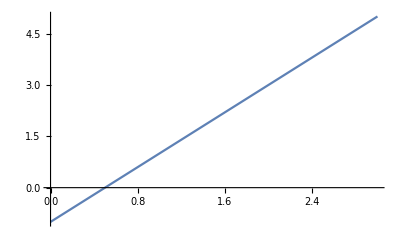

```mathematica
Plot[a0+a1*t,{t,0,3}]
```

## An n^th degree polynomial through n+1 data points

We can generalize (1) for a polynomial of degree n: p(t)=a0+a1t+ ... +ant^ngoing through n+1 data points: (x0,y0),(x1,y1), ..., (xn,yn) as follows

p(x0) = y0
p(x1) = y1

p(xn) = yn

To solve this system of linear equations we need to form our coefficient matrix A and right hand side vector y. The right hand side vector y is simple: y={{y0},{y1},...,{yn}}. To form the coefficient matrix A, we must first decide what basis for the set of all polynomials of degree n or less we are using. Let us start with the monomial basis: 1, t, t^2, ..., t^n, we will denote these basis polynomials as b0(t), b1(t), ..., bn(t), respectively. Then, the coefficient matrix A can be defined by its individual entries

aij=bj(xi) for i=1,2,...,n+1 and j=1,2,...,n+1.

The following function SVM (Standard Vandermonde matrix) takes on a vector x whose entries are the independent data values and returns the coefficient matrix A, as defined in (4).

```mathematica
SVM[x_]:=
Module[{n,A},
n=Dimensions[x][[1]];
A=ConstantArray[1.,{n,n}];
Do[A[[All,j]]=A[[All,j-1]]*x,{j,2,n}];
A]
```

As an example, we will create (n+1) data points between -1 and 1 using the Range command. Then, we will create the coefficient matrix A, and show it using MatrixForm.

```mathematica
n=8;
x=Range[-1,1,2/n];
A=SVM[x];
MatrixForm[A]
```

(1. | -1. | 1. | -1. | 1. | -1. | 1. | -1. | 1.
1. | -0.75 | 0.5625 | -0.421875 | 0.316406 | -0.237305 | 0.177979 | -0.133484 | 0.100113
1. | -0.5 | 0.25 | -0.125 | 0.0625 | -0.03125 | 0.015625 | -0.0078125 | 0.00390625
1. | -0.25 | 0.0625 | -0.015625 | 0.00390625 | -0.000976563 | 0.000244141 | -0.0000610352 | 0.0000152588
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0.25 | 0.0625 | 0.015625 | 0.00390625 | 0.000976563 | 0.000244141 | 0.0000610352 | 0.0000152588
1. | 0.5 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125 | 0.00390625
1. | 0.75 | 0.5625 | 0.421875 | 0.316406 | 0.237305 | 0.177979 | 0.133484 | 0.100113
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

Next, we will create a set of dependent data points based on the Cos[x]. Then, we will solve the corresponding matrix equation using LinearSolve, which will return the coefficients of the n^th degree polynomial that interpolates this data set.

```mathematica
y=Cos[2*Pi*x];
coeff=LinearSolve[A,y]
```

{1.,1.26319×10^-15,-19.6063,-3.78956×10^-14,61.8667,1.01055×10^-13,-68.2667,-6.44225×10^-14,26.0063}

In order to evaluate this polynomial we need to take the dot product of coeff with {1,t,t^2, ..., t^n}. To this end, we define the following function MB (Monomial Basis) which creates the latter list.

```mathematica
MB[t_,n_]:=
Module[{b},
b=ConstantArray[1.,{n+1}];
Do[b[[j]]=t*b[[j-1]],{j,2,n+1}];
b];
```

Now, we can plot are polynomial interpolate

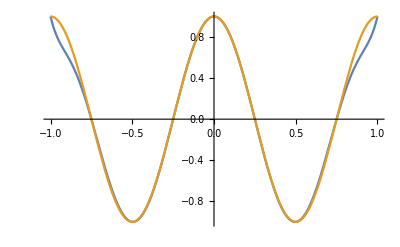

```mathematica
Plot[{coeff.MB[t,n],Cos[2*Pi*t]},{t,-1,1}]
```

Well that is not bad at all. Given 9 data points, we are able to closely fit a polynomial of degree 8 to the function Cos[2*Pi*t]  over the interval [-1,1]. At this point, it may seem that working with the monomial basis is not so bad. To show the problems that we can have let us increase the frequency of our Cosine function, thereby making it wigglier, and multiply by Exp, thereby making it have varied amplitude.

```mathematica
Clear[x]
x[n_]:=Range[-1,1,2/n];
Manipulate[
A=SVM[x[n]];
y=Exp[x[n]]*Cos[17*Pi*x[n]];
coeff=LinearSolve[A,y];
Plot[{coeff.MB[t,n],Exp[t]*Cos[17*Pi*t]},{t,-1,1}],{n,5,30,1}]
```

## The Chebyshev Polynomial and Chebyshev Points